```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/mkononen/git/quantum-utils-mathematica/test/benchmarks/GRAPE

```mathematica
Needs["QuantumUtils`"]
Needs["StripLineResonator`"]
```

```mathematica
LaunchKernels[]
```

{KernelObject[1,local],KernelObject[2,local]}

### Parameters

```mathematica
maxVoltage=1(*V*);
γe=2.8*10^6*2*π;

SelectMode[$onePort];

Parameters[$onePort,"linear"]={
	l->168.9pH,                 
	r->0.01Ω,
	c->1.47856 pF,
	cm->0.021256 pF,
	rs->50Ω,
	scale->19*0.838 10^11 MHz/Wb (* Calibrated to give 360 rotation in 100 ns (10 MHz Rabi) at full Pulse Amplitude*)
};

Parameters[$onePort,"nonlinear"]={
	l->168.9pH * (1+αL*Abs[il]^2),
	r->0.01Ω,
	c->1.47856 pF,
	cm->0.021256 pF,
	rs->50Ω,
	scale->1.9*0.838 10^12 MHz/Wb (* Calibrated to give 360 rotation in 100 ns (10 MHz Rabi) at full Pulse Amplitude*) (*NOTE: I've changed from 0.838 10^11 to ^13*)
}/.{
	αL->(0.01/amp^2)
};
```

```mathematica
ω1= 10γe;
ωc = 3500γe;
ω0 = 3200γe;
dt = 5.0ns;
```

### Create initial pulse

#### Parameters

```mathematica
controlRange = 1.{{ ω0+50*2.8 *10^6*2*π,ωc+25*2.8 *10^6*2*π}}; 
ta = 750*10^-9;Nta = IntegerPart[ta/dt ];
tp=500*10^-9; Ntp = IntegerPart[tp/dt];
dtran = 0.01;Ntr = 200;
```

#### Pulse for ω_1 (x-direction)

```mathematica
f[x_] =Piecewise[{{0,x<100},{1,700>x>100}}];
g[x_] = PiecewiseExpand[Piecewise[{{f[x],x<700},{0,x>700}}]];
```

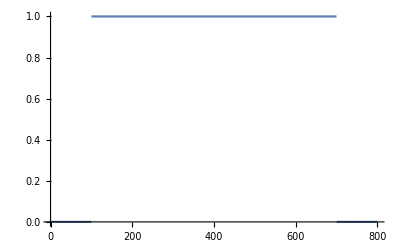

```mathematica
Plot[g[x],{x,0,800}]
```

#### Pulse for ω_0

Set::take: Cannot take positions 75 through 375 in {{5.×10^-9,5.63356×10^10},{5.×10^-9,5.63692×10^10},{5.×10^-9,5.64265×10^10},{5.×10^-9,5.65194×10^10},{5.×10^-9,5.66627×10^10},{5.×10^-9,5.68724×10^10},«40»,{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},«51»}.

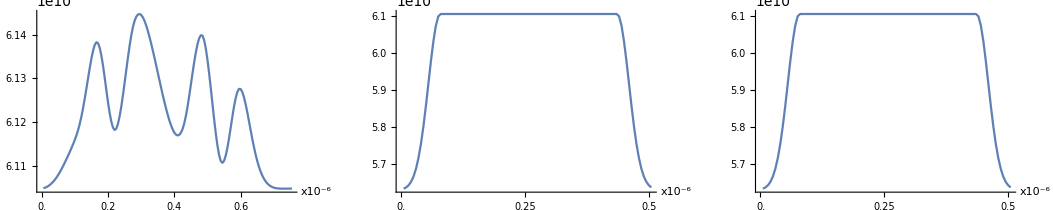

Part::take: Cannot take positions 50 through 150 in {{5.×10^-9,5.63356×10^10},{5.×10^-9,5.63692×10^10},{5.×10^-9,5.64265×10^10},{5.×10^-9,5.65194×10^10},{5.×10^-9,5.66627×10^10},{5.×10^-9,5.68724×10^10},«40»,{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},«51»}.

| gate Pulse | gate Pulse (gate) | What we want (total) | What we want (gate)
Max val | 6.10474×10^10 | {{5.×10^-9,5.63356×10^10},{5.×10^-9,5.63692×10^10},{5.×10^-9,5.64265×10^10},{5.×10^-9,5.65194×10^10},{5.×10^-9,5.66627×10^10},{5.×10^-9,5.68724×10^10},{5.×10^-9,5.71634×10^10},{5.×10^-9,5.75454×10^10},{5.×10^-9,5.80182×10^10},{5.×10^-9,5.8568×10^10},{5.×10^-9,5.9164×10^10},{5.×10^-9,5.97604×10^10},{5.×10^-9,6.03004×10^10},{5.×10^-9,6.07249×10^10},{5.×10^-9,6.09832×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.09832×10^10},{5.×10^-9,6.07249×10^10},{5.×10^-9,6.03004×10^10},{5.×10^-9,5.97604×10^10},{5.×10^-9,5.9164×10^10},{5.×10^-9,5.8568×10^10},{5.×10^-9,5.80182×10^10},{5.×10^-9,5.75454×10^10},{5.×10^-9,5.71634×10^10},{5.×10^-9,5.68724×10^10},{5.×10^-9,5.66627×10^10},{5.×10^-9,5.65194×10^10},{5.×10^-9,5.64265×10^10},{5.×10^-9,5.63692×10^10}}⟦50;;150,2⟧ | 6.2103×10^10 | 6.2103×10^10
Min val | 5.63356×10^10 | {{5.×10^-9,5.63356×10^10},{5.×10^-9,5.63692×10^10},{5.×10^-9,5.64265×10^10},{5.×10^-9,5.65194×10^10},{5.×10^-9,5.66627×10^10},{5.×10^-9,5.68724×10^10},{5.×10^-9,5.71634×10^10},{5.×10^-9,5.75454×10^10},{5.×10^-9,5.80182×10^10},{5.×10^-9,5.8568×10^10},{5.×10^-9,5.9164×10^10},{5.×10^-9,5.97604×10^10},{5.×10^-9,6.03004×10^10},{5.×10^-9,6.07249×10^10},{5.×10^-9,6.09832×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.10474×10^10},{5.×10^-9,6.09832×10^10},{5.×10^-9,6.07249×10^10},{5.×10^-9,6.03004×10^10},{5.×10^-9,5.97604×10^10},{5.×10^-9,5.9164×10^10},{5.×10^-9,5.8568×10^10},{5.×10^-9,5.80182×10^10},{5.×10^-9,5.75454×10^10},{5.×10^-9,5.71634×10^10},{5.×10^-9,5.68724×10^10},{5.×10^-9,5.66627×10^10},{5.×10^-9,5.65194×10^10},{5.×10^-9,5.64265×10^10},{5.×10^-9,5.63692×10^10}}⟦50;;150,2⟧ | 5.62973×10^10 | 6.10474×10^10

```mathematica
auxRange = 1.{{ 0,30*2.8 *10^6*2*π}}; 
auxiliarPulse = RandomSmoothPulse[dt,Nta+1,auxRange];
auxiliarPulse[[All,2]]=MapThread[Times,{GaussianTailsPulse[dt,ta,ta/4,Max->1][[All,2]],auxiliarPulse[[All,2]]}] +ωc-30*2.8 *10^6*2*π;
plt1 =ListLinePlot[auxiliarPulse[[All,2]],Ticks->{Transpose[{Range[0,Length[auxiliarPulse],20],N[dt*10^6*Range[0,Length[auxiliarPulse],20]]}],Automatic},AxesLabel->{"x10^-6",None}];
(*Create gaussian tails*)
GaussianEnvelope = GaussianTailsPulse[dt,tp,tp/7,Max->ωc-30*2.8 *10^6*2*π-ω0]+ω0; 
plt2 = ListLinePlot[GaussianEnvelope[[All,2]],Ticks->{Transpose[{Range[0,Length[GaussianEnvelope],50],N[dt*10^6*Range[0,Length[GaussianEnvelope],50]]}],Automatic},AxesLabel->{"x10^-6",None}];
(*Merge the two pulses to create the initial guess*)
Pulseω0 = RandomSmoothPulse[dt,Ntp+1,auxRange]; Pulseω0[[All,2]]=GaussianEnvelope[[All,2]];
Pulseω0[[75;;375,2]]=auxiliarPulse[[All,2]];
plt3 = ListLinePlot[Pulseω0[[All,2]],Ticks->{Transpose[{Range[0,Length[Pulseω0],50],N[dt*10^6*Range[0,Length[Pulseω0],50]]}],Automatic},AxesLabel->{"x10^-6",None}];
GraphicsGrid[{{plt1,plt2,plt3}}]
tab = { {TextCell[""],TextCell["gate Pulse"],TextCell["gate Pulse (gate)"],TextCell["What we want (total)"],TextCell["What we want (gate)"]},
	 {TextCell["Max val"],Max[Pulseω0[[All,2]]],Max[Pulseω0[[50;;150,2]]],ωc+30*2.8 *10^6*2*π,ωc+30*2.8 *10^6*2*π},
	   {TextCell["Min val"],Min[Pulseω0[[All,2]]],Min[Pulseω0[[50;;150,2]]],ω0,ωc-30*2.8 *10^6*2*π}};
Grid[tab,Frame->All]
(*Add constant ω0 term to the ω0 Pulse*)
Pulseω0=Join[Table[{1/(2*10^8),Pulseω0[[1,2]]},{x,1,Ntr+0.2*Ntr,1}],Pulseω0];
Pulseω0=Join[Pulseω0,Table[{1/(2*10^8),Pulseω0[[1,2]]},{x,1,Ntr-0.2*Ntr,1}]];
```

```mathematica
Length[auxiliarPulse]
Length[GaussianEnvelope]
```

151

101

#### Initial Guess

```mathematica
initialGuess=Table[{5ns,g[i],0.,Pulseω0[[i,2]]},{i,1,Ntp+2*Ntr+1}];
Ntotal=Length[initialGuess]
```

501

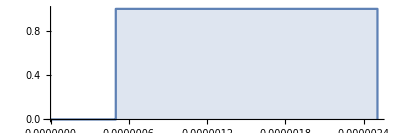
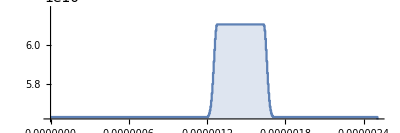

```mathematica
{First@@PulsePlot[ToPulse[initialGuess],PlotRange-> {All,{0,1}},AspectRatio-> 1/3],Last@@PulsePlot[ToPulse[initialGuess],PlotRange-> {All,{ω0-10*2.8*π*10^6,ωc+30*2.8*π*10^6}},AspectRatio-> 1/3]}
```

### Internal Hamiltonian, Control Hamiltonian and target unitary

We are adding a new control Hamiltonian to our initial set. The distortion operator applied to TP[X] induces a pulse in the direction σ_y.

```mathematica
Utarget = MatrixExp[-I(π/2)TP[X]/2];
Hint = -1/2 (ωc-δω) TP[Z];
Hcontrol = {1/2 TP[X],1/2TP[Y],1/2  TP[Z]};
```

### Distortion operators

```mathematica
samplingRate=2.5ns;
ringdownTime=100ns;
controlRange = maxVoltage*{{-1,1},{-1,1}};  
τc=10^-8;
```

```mathematica
ClearAll@ringDownDistortion;
ringDownDistortion=
ResonatorRingdownDistortion[
1, (* I believe this is the number of compensation steps? *)
Parameters["nonlinear"],
CompensationTimeSteps->{ringdownTime}, (* this is equivalent to ringdownTime in linear example when DecayRatio is set to 0 *) 
DecayRatio->0, (* Setting this to zero eliminates ringdown compensation *)
RiseTime->0.2ns,
SamplingInterval->samplingRate,
MaxSteps->10^6,
AmplitudeRange->controlRange
];
```

```mathematica
Clear[distortion]
distortion=DistortionOperator[
Function[{pulse,computeJac},
Module[{zpulse,xypulse,M,L,N,K,f,AUX,x,zdistortion},
xypulse=ringDownDistortion[pulse⟦All,1;;3⟧,computeJac];
If[computeJac,
{
{M,L,N,K}=Dimensions[xypulse⟦2⟧];

zdistortion=ExponentialDistortion[τc,Length[pulse],M,pulse⟦1,1⟧,samplingRate];
zpulse=zdistortion[pulse⟦All,{1,4}⟧,computeJac];

Append[xypulse⟦1⟧ᵀ,zpulse⟦1,All,2⟧]ᵀ,

f=Function[x,Transpose[Append[Transpose[ArrayReshape[x,{L+1,K}]],{0.,0.,0.}]]];
AUX=Transpose[xypulse⟦2⟧,{1,3,2,4}];
Table[AUX⟦i,j⟧={AUX⟦i,j⟧},{i,1,M},{j,1,N}];
AUX=Apply[f,AUX,{2}];
Table[AUX⟦i,j⟧⟦L+1,K+1⟧=ArrayReshape[ArrayReshape[zpulse⟦2⟧,{1,N*M}]⟦1⟧,{M,N}]⟦i,j⟧,{i,1,M},{j,1,N}];
Transpose[AUX,{1,3,2,4}] 
},
 M=Length[xypulse];

zdistortion=ExponentialDistortion[τc,Length[pulse],M,pulse⟦1,1⟧,samplingRate];
zpulse=zdistortion[pulse⟦All,{1,4}⟧,computeJac];

Append[xypulseᵀ,zpulse⟦All,2⟧]ᵀ
]
]
],
"JointDistortion"
]
```

JointDistortion

```mathematica
distortedPulse=distortion[initialGuess,False]; //AbsoluteTiming
Dimensions[Last@distortedPulse]
```

{172.992,Null}

{4}

```mathematica
plt1=First@@PulsePlot[ToPulse[distortedPulse],PlotRange-> {All,{-1,1.2*10^8}},AspectRatio-> 1/3,PlotLabel-> "Distorted Initial Control X"];
plt2=Last@Take[First@PulsePlot[ToPulse[distortedPulse],PlotRange-> {All,{1,-1.2*10^8}},AspectRatio-> 1/3,PlotLabel-> "Distorted Initial Control Y"],2];
plt3=Last@@PulsePlot[ToPulse[distortedPulse],PlotRange-> {All,{ω0-10*2.8*π*10^6,ωc+30*2.8*π*10^6}},AspectRatio-> 1/3,PlotLabel-> "Distorted Initial Control Z"];
```

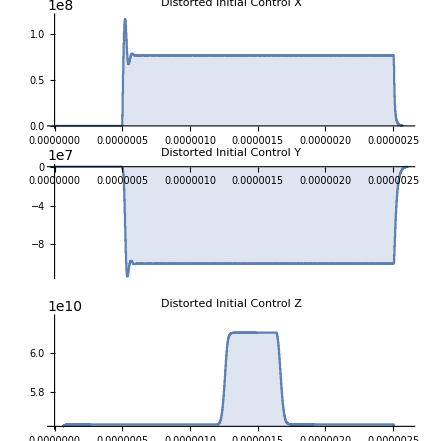

```mathematica
GraphicsGrid[{{plt1},{plt2},{plt3}}]
```

### Optimization

```mathematica
controlRange = 1.{{-1.,1.},{-1.,1.},{ ω0-40*2.8 *10^6*2*π,ωc+45*2.8 *10^6*2*π}}; 
mask= Table[{0,0,0},{x,1,Length[initialGuess],1}];
mask[[53;;107,3]]=1;
```

```mathematica
dist=UniformParameterDistribution[δω->{0,1γe,10}];
```

```mathematica
Profile[
FindPulse[
initialGuess,
Utarget,
0.999,
controlRange,
Hcontrol,
Hint,
DerivativeMask-> mask,
(* DistortionOperator-> distortion, *)
ParameterDistribution-> dist,
VerboseAscent-> True, 
SkipChecks -> True
]
]
```

#rawUtilitypenaltyimprovementstepSizebestMultbetaResetCttoc (ms)

10.27433400.2743340.0008056560.64908208774.599

20.27449400.0001601750.000805656108694.113

30.2744940-1.46549×10^-130.0007220940.8033219065.849

40.27449408.14153×10^-110.0007453941.0655719332.766

50.27449401.27676×10^-150.000745394128838.14

60.2744940-1.38778×10^-150.000745394139142.375

70.2744940-1.38778×10^-150.000745394149486.056

80.2744940-1.38778×10^-150.000745394159306.455

90.2744940-1.38778×10^-150.000745394168744.857

100.2744940-1.38778×10^-150.000745394178738.955

Head | Value
UtilityValue | 0.274494
PenaltyValue | 0
ExitMessage | The average improvement over 5 iterations was less than MinimumImprovement.
Target | (1/(√2) | -ⅈ/(√2)
-ⅈ/(√2) | 1/(√2))
InternalHamiltonian | (1/2 (-6.15752×10^10+δω) | 0
0 | (6.15752×10^10-δω)/2)
ControlHamiltonians | (0 | 1/2
1/2 | 0),(0 | -ⅈ/2
ⅈ/2 | 0),(1/2 | 0
0 | -1/2)
AmplitudeRange | {{-1.,1.},{-1.,1.},{5.55936×10^10,6.23669×10^10}}
TimeSteps | {1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000,1/200000000}
Pulse | (0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63352×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63692×10^10 | 5.64265×10^10 | 5.65194×10^10 | 5.66627×10^10 | 5.68724×10^10 | 5.71634×10^10 | 5.75454×10^10 | 5.80182×10^10 | 5.8568×10^10 | 5.9164×10^10 | 5.97604×10^10 | 6.03004×10^10 | 6.07249×10^10 | 6.09832×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.10474×10^10 | 6.09832×10^10 | 6.07249×10^10 | 6.03004×10^10 | 5.97604×10^10 | 5.9164×10^10 | 5.8568×10^10 | 5.80182×10^10 | 5.75454×10^10 | 5.71634×10^10 | 5.68724×10^10 | 5.66627×10^10 | 5.65194×10^10 | 5.64265×10^10 | 5.63692×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10 | 5.63356×10^10)
ParameterDistribution | {{1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10},{{δω→-1.75929×10^7},{δω→-1.36834×10^7},{δω→-9.77384×10^6},{δω→-5.86431×10^6},{δω→-1.95477×10^6},{δω→1.95477×10^6},{δω→5.86431×10^6},{δω→9.77384×10^6},{δω→1.36834×10^7},{δω→1.75929×10^7}}}
DistortionOperator | IdentityDistortion[]
PulsePenalty | ZeroPenalty[]

```mathematica
pulse = FindPulse[
initialGuess,
Utarget,
0.999,
controlRange,
Hcontrol,
Hint,
DerivativeMask-> mask,
DistortionOperator-> distortion,
ParameterDistribution-> dist,
VerboseAscent-> True, 
SkipChecks -> True
]
```

#rawUtilitypenaltyimprovementstepSizebestMultbetaResetCttoc (ms)

$Aborted

```mathematica
BlochPlot[{States@PulseSim[Hint/.δω-> -1*2.8*10^6*2*π,SimForm[pulse,True],PollingInterval-> 1ns, InitialState-> TP[U]],States@PulseSim[Hint/.δω-> 0*2.8*10^6*2*π,SimForm[pulse,True],PollingInterval-> 1ns, InitialState-> TP[U]],States@PulseSim[Hint/.δω-> 1*2.8*10^6*2*π,SimForm[pulse,True],PollingInterval-> 1ns, InitialState-> TP[U]]
},
BlochPlotJoined-> True]
```

-Graphics3D-